{{x→InterpolatingFunction[…]}}

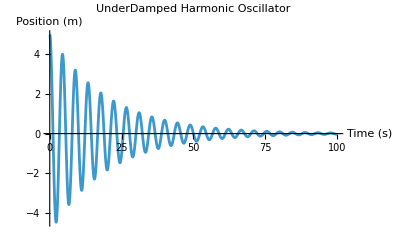

```mathematica
Clear[x];
m=10;
k=20;
b=1;
x0=5;
v0=0;
sol=NDSolve[{x''[t]+(b/m) x'[t]+(k/m) x[t]==0,x[0]==x0,x'[0]==v0},x,{t,0,100}]
Plot[Evaluate[x[t]/. sol],{t,0,100},PlotLabel->"UnderDamped Harmonic Oscillator",AxesLabel->{"Time (s)","Position (m)"},PlotRange->All]
```

The damping parameters are below the critical threshold (γ < 2ω0). This causes the system to oscillate with an amplitude that decreases over time.

{{x→InterpolatingFunction[…]}}

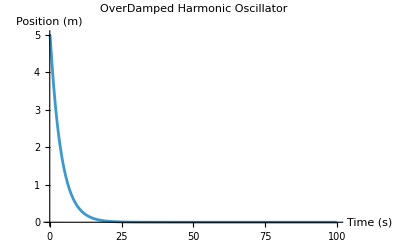

```mathematica
Clear[x];
m=10;
k=20;
b=80;
x0=5;
v0=0;
sol=NDSolve[{x''[t]+(b/m) x'[t]+(k/m) x[t]==0,x[0]==x0,x'[0]==v0},x,{t,0,100}]
Plot[Evaluate[x[t]/. sol],{t,0,100},PlotLabel->"OverDamped Harmonic Oscillator",AxesLabel->{"Time (s)","Position (m)"},PlotRange->All]
```

{{x→InterpolatingFunction[…]}}

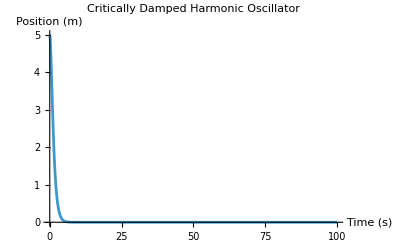

```mathematica
Clear[x];
m=10;
k=20;
b=28.2842712474619;
x0=5;
v0=0;
sol=NDSolve[{x''[t]+(b/m) x'[t]+(k/m) x[t]==0,x[0]==x0,x'[0]==v0},x,{t,0,100}]
Plot[Evaluate[x[t]/. sol],{t,0,100},PlotLabel->"Critically Damped Harmonic Oscillator",AxesLabel->{"Time (s)","Position (m)"},PlotRange->All]
```

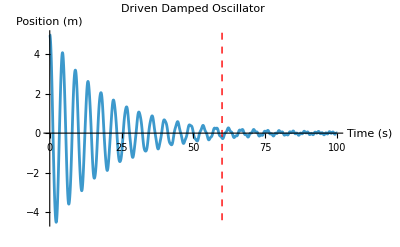

```mathematica
Clear[x,sol];
m=10;
k=20;
b=1;
x0=5;
v0=0;
wd=5;
F0=10;

sol=NDSolve[{x''[t]+(b/m) x'[t]+(k/m) x[t]==(F0/m) Cos[wd t],x[0]==x0,x'[0]==v0},x,{t,0,100}];

Plot[Evaluate[x[t]/. sol],{t,0,100},PlotLabel->"Driven Damped Oscillator",AxesLabel->{"Time (s)","Position (m)"},PlotRange->All,Epilog->{Red,Dashed,InfiniteLine[{{60,0},{60,1}}]}]
```

{{x→InterpolatingFunction[…]}}

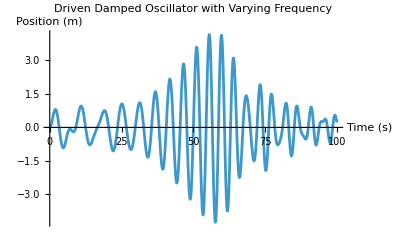

```mathematica
Clear[x,sol];
m=10;
k=20;
b=1;
F0=10;
x0=0;
v0=0;

sol=NDSolve[{x''[t]+(b/m) x'[t]+(k/m) x[t]==(F0/m) Cos[(0.5+0.01*t)*t],x[0]==x0,x'[0]==v0},x,{t,0,100}]

Plot[Evaluate[x[t]/. sol],{t,0,100},PlotLabel->"Driven Damped Oscillator with Varying Frequency",AxesLabel->{"Time (s)","Position (m)"},PlotRange->All]
```

{{x→InterpolatingFunction[…]}}

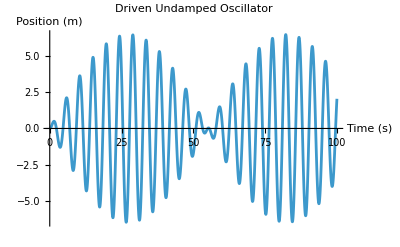

```mathematica
Clear[x,sol];
m=10;
k=20;
b=0;
F0=10;
wd=1.3;
x0=0;
v0=0;

sol=NDSolve[{x''[t]+(b/m) x'[t]+(k/m) x[t]==(F0/m) Cos[wd t],x[0]==x0,x'[0]==v0},x,{t,0,100}]

Plot[Evaluate[x[t]/. sol],{t,0,100},PlotLabel->"Driven Undamped Oscillator",AxesLabel->{"Time (s)","Position (m)"},PlotRange->All]
```